# Hard X-Rays Tracing

## 2 - Dimensional Case

```mathematica
Experimental data
```

```mathematica
files=FileNames[{"*.txt","*.txt_psd"},NotebookDirectory[]];
PSD1Dinit= Import[#,"Table"]&[Part[Select[#,StringEndsQ[#,"80x80um.txt_psd"]&]&@files,1]];
SurfaceVal=-0.049Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];(*nm*)
Surfacepts:=Transpose[{ 10^3 Range[0,80,80/511],SurfaceVal[[#]]}]&(*nm*)
SurfaceFunc= Interpolation[Surfacepts[1], Method-> "Spline"];
σ=Mean[RootMeanSquare[SurfaceVal]];
```

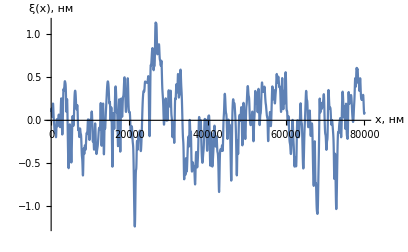

```mathematica
Plot[SurfaceFunc[x],{x,0.,80000.},PlotRange->All,AxesStyle->Directive[15,Bold],AxesLabel->{Style["x, нм",Gray,15],Style["ξ(x), нм",Gray,15]}]
```

```mathematica
PSD-function
```

```mathematica
PSD1D=Mean[80/512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dfunc=GeneralizedLinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,{1,x,x^2,x^3},x,ExponentialFamily->"Gamma"];(*μm^3*)
```

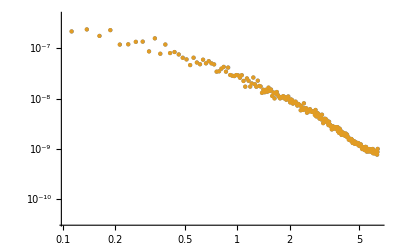

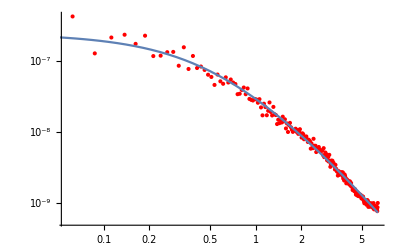

```mathematica
ListLogLogPlot[{{Range[1/80,511/80,1/40],PSD1D}//Transpose,PSD1Dinit},PlotStyle->PointSize[Medium]]
Show[ListLogLogPlot[PSD1Dinit,PlotStyle->Red],LogLogPlot[PSD1Dfunc[x],{x,1/80,511/80}]]
```

```mathematica
Dielectric Permittivity
```

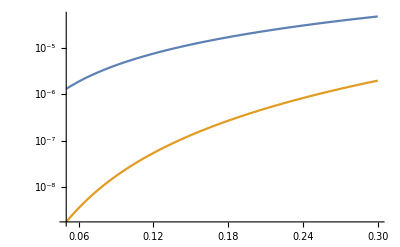

```mathematica
IndexRefr = Drop[Import[#,"Table"],2]&[Part[Select[#,StringEndsQ[#,"Index of Refraction.txt"]&]&@files,1]];
δ = Interpolation[{IndexRefr[[All,1]],IndexRefr[[All,2]]}//Transpose,Method-> "Spline"];
γ = Interpolation[{IndexRefr[[All,1]],IndexRefr[[All,3]]}//Transpose,Method-> "Spline"];
ε[λ_]:=1-δ[λ](*λ [nm]*)
εε[λ_]:=1-δ[λ]+ⅈ γ[λ](*λ [nm]*)
LogPlot[{δ[x],γ[x]},{x,0.05,0.3}]
```

```mathematica
The Scattering Indicatrix
```

```mathematica
k=(2π)/#&;
t=(2 Sin[#])/(Sin[#]+√(ε[#2]-Cos[#]^2))&;
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dfunc[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]]
λ0 = 0.162;(*nm*)
θ0 = Abs[1-ε[λ0]]^(1/2);
AΠ[θinc_,λ_]:=AΠ[θinc,λ]=NIntegrate[Π[θ,θinc,λ],{θ,0,θ0,θinc,π/2}]
P[θ_,θ0_,λ_]:=Π[θ,θ0,λ]/AΠ[θ0,λ]
```

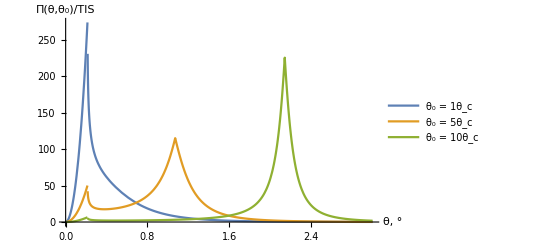

```mathematica
Plot[P[n °,# θ0,λ0]&/@{1,5,10}//Evaluate,{n ,0,3},PlotRange->All,AxesStyle->15,AxesLabel->{Style["θ, °",Gray,15],Style["Π(θ,θ_0)/TIS",Gray,15]},PlotLegends->{"θ_0 = "<>ToString[#]<>"θ_c"&/@{1,5,10}}]
```

```mathematica
The Fresnel's Equations
```

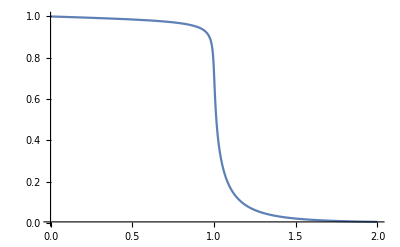

```mathematica
Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&
Plot[Rf[n θ0,λ0],{n,0,2},PlotRange->Full]
Π2:=P[#,#2,#3]Rf[#2,#3]&
```

```mathematica
Total Integrated Scattering
```

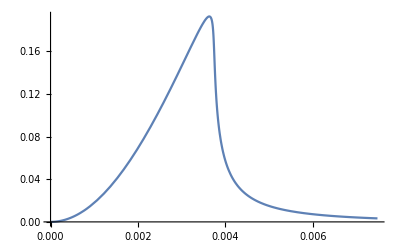

```mathematica
TIS[θ0_,λ_,h_:1]:=Rf[θ0,λ](1-Exp[-((4π h σ Sin[θ0])/λ)^2])
Rs[θ0_,λ_,h_:1]:=Rf[θ0,λ]Exp[-((4π h σ Sin[θ0])/λ)^2]
Plot[TIS[x,λ0,5],{x,0,2θ0},PlotRange->Full]
```

```mathematica
PSD model
```

```mathematica
PSD1Dm=NonlinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{ξ,α}={ξξ,αα}/.PSD1Dm["BestFitParameters"];
Πm[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]]
AΠm[θinc_,λ_]:=AΠm[θinc,λ]=NIntegrate[Πm[θ,θinc,λ],{θ,0,θ0,θinc,π/2}]
Pm[θ_,θ0_,λ_]:=Πm[θ,θ0,λ]/AΠm[θ0,λ]
```

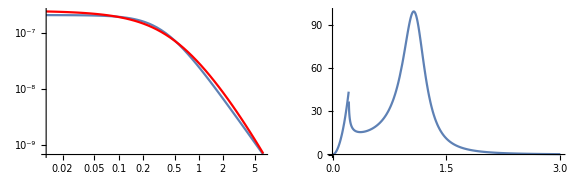

```mathematica
GraphicsRow[{Show[LogLogPlot[PSD1Dm[x],{x,1/80,511/80}],LogLogPlot[PSD1Dfunc[x],{x,1/80,511/80},PlotStyle->Red],PlotRange->All],Plot[Pm[n °,5θ0,λ0],{n ,0,3},PlotRange->All]},ImageSize->Large]
```

```mathematica
Random Number Generator
```

```mathematica
mydist[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"]
mydistm[y_]:=ProbabilityDistribution[Πm[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"]
```

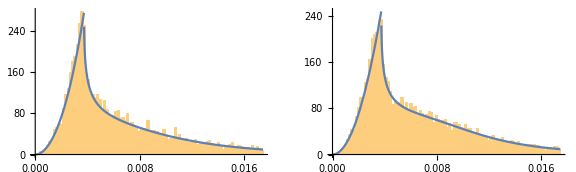

```mathematica
GraphicsRow[{Show[Histogram[RandomVariate[mydist[θ0],10000],{0°,1°,0.01°},"ProbabilityDensity"],Plot[P[x,θ0,λ0],{x,0,1°},PlotRange->All],AxesOrigin->{0,0}],Show[Histogram[RandomVariate[mydistm[θ0],10000],{0°,1°,0.01°},"ProbabilityDensity"],Plot[Pm[x,θ0,λ0],{x,0,1°},PlotRange->All],AxesOrigin->{0,0}]},ImageSize->Large]
```

```mathematica
The Experiment Geometry
```

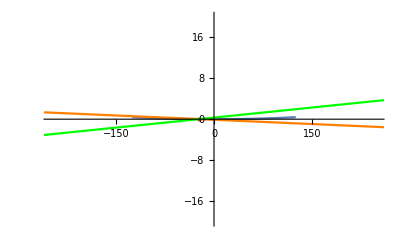

```mathematica
ρ=20000 (*мм*);(*Радиус кривизны зеркала*)
d = 250(*мм*);(*Диаметр зеркала*)
L=400(*мм*);(*Расстояние от источника до зеркала*)
R=185(*мм*);(*Расстояние от зеркала до детектора*)
ψ=2.ArcSin[d/(2ρ)];(*Угол раствора зеркала*)
φ=RandomReal[{-ψ/2,ArcTan[-(Tan[ψ/2](L-d/2))/L]}];
n=(ρ ψ)/(80 10^-3);
dmax=0.025;
line[x_,linepar_]:=linepar[[2]]+Tan[linepar[[3]]](x-linepar[[1]])
initlpar:={-L,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2),φ};
pts:=Quiet[MaximalBy[Select[NSolve[{x==ρ Cos[θ],y==ρ Sin[θ]+ρ,y==line[x,#]},{x,y,θ}],-π/2-ψ/2≤(θ/.#)≤-π/2+ψ/2 &],θ/.#&][[1]]]&
Show[{ParametricPlot[{ρ Cos[θ],ρ Sin[θ]+ρ},{θ,-π/2-ψ/2,-π/2+ψ/2}],Graphics[{Red,PointSize[Medium],Point[{x,y}/.pts[initlpar]]}],Plot[line[xx,initlpar],{xx,x-L/.pts[initlpar],x+L/.pts[initlpar]},PlotStyle->Orange],Plot[line[xx,#],{xx,x-L/.pts[initlpar],x+L/.pts[initlpar]},PlotStyle->Green]&@({x,y,θ+π/2+RandomVariate[mydist[(θ+π/2-φ)/.pts[initlpar]]]}/.pts[initlpar])},AspectRatio->1/GoldenRatio,PlotRange->{{-d,d},{-20,20}}]
```

```mathematica
Ray Tracing Demonstration
```

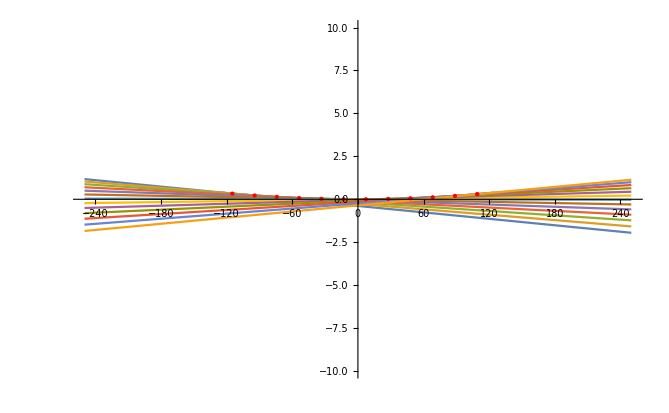

{0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.00018823,0.000189556}

```mathematica
initlpar={-L,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+RandomReal[{0,dmax}],-ψ/2};
NestWhileList[(sw=RandomReal[];If[sw<(TIS[θ+π/2-#[[3]],λ0]/.pts[#]),{x,y,θ+π/2+RandomVariate[mydistm[θ+π/2-#[[3]]]]}/.pts[#],{x,y,2θ+π-#[[3]]}/.pts[#]])&,initlpar,(fl=Boole[sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])];sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])&&({x,y,θ}/.#&)@pts[#1]≠({x,y,θ}/.#&)@pts[#2])&,2];
Show[ParametricPlot[{ρ Cos[θ],ρ Sin[θ]+ρ},{θ,-π/2-ψ/2,-π/2+ψ/2}],Plot[line[xx,#]&/@%//Evaluate,{xx,-d,d}],Graphics[{Red,PointSize[Medium],Point[{x,y}/.pts/@%]}],AspectRatio->1/GoldenRatio,PlotRange->{{-d,d},{-10,10}}]
TIS[#,λ0]&@(θ+π/2-#[[3]]/.pts[#])&/@%%
```

```mathematica
Ray Tracing Core
```

```mathematica
Res[len_,h_:σ]:=Module[{SurfaceVal,PSD1D,PSD1Dfunc,Π,σ,TIS,mydist,partable,j},
SurfaceVal=-0.049(h/Mean[RootMeanSquare[-0.049Import[Select[files,StringEndsQ[#,"80x80um.txt"]&][[1]],"Table"][[17;;]]]]) Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];
PSD1D=Mean[80/512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dfunc=GeneralizedLinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,{1,x,x^2,x^3},x,ExponentialFamily->"Gamma"];
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dfunc[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
σ=Mean[RootMeanSquare[SurfaceVal]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π σ Sin[θ0])/λ)^2]);
mydist[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"];
SetSharedVariable[j];
j=0;
partable=Monitor[ParallelTable[j++;{NestWhile[(sw=RandomReal[];If[sw<(TIS[θ+π/2-#[[3]],λ0]/.pts[#]),{x,y,θ+π/2+RandomVariate[mydist[θ+π/2-#[[3]]]]}/.pts[#],{x,y,2θ+π-#[[3]]}/.pts[#]])&,{-L,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+RandomReal[{0,dmax}],-ψ/2},(fl=Boole[sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])];sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])&&({x,y,θ}/.#&)@pts[#1]≠({x,y,θ}/.#&)@pts[#2])&,2],fl},{i,1,len}],ProgressIndicator[j,{1,len}]];
Select[Pick[partable[[All,1]],partable[[All,2]],1],NumberQ[#[[3]]]&]
]//Quiet
Resm[N_,σ_:σ,ξ_:ξ]:=Module[{PSD1Dmodel,Π,TIS,mydist,partable,j},
PSD1Dmodel[p_]:=2/(√π)Gamma[1/2+α]/Gamma[α](σ^2 ξ 10^-6)/((1+p^2 ξ^2)^(1/2+α));
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dmodel[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π σ Sin[θ0])/λ)^2]);
mydist[y_]:=ProbabilityDistribution[Π[x,yy,λ0],{x,0,89°},Assumptions->yy>0&&yy<89°,Method->"Normalize"]/.yy->y;
SetSharedVariable[j];
j=0;
partable=Monitor[ParallelTable[j++;{NestWhile[(sw=RandomReal[];If[sw<(TIS[θ+π/2-#[[3]],λ0]/.pts[#]),{x,y,θ+π/2+RandomVariate[mydist[θ+π/2-#[[3]]]]}/.pts[#],{x,y,2θ+π-#[[3]]}/.pts[#]])&,{-L,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+RandomReal[{0,dmax}],-ψ/2},(fl=Boole[sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])];sw<Rf[#,λ0]&@(θ+π/2-#1[[3]]/.pts[#1])&&({x,y,θ}/.#&)@pts[#1]≠({x,y,θ}/.#&)@pts[#2])&,2],fl},{i,1,N}],ProgressIndicator[j,{1,N}]];
Select[Pick[partable[[All,1]],partable[[All,2]],1],NumberQ[#[[3]]]&]
]//Quiet
```

```mathematica
Results Calculation
```

```mathematica
Res[10000,9]>>res1
Res[10000,6]>>res2
Res[10000,3]>>res3
Res[10000,0]>>res4
```

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Res[10000,1]>>res5
Res[10000,2]>>res6
Res[10000,3]>>res7
Res[10000,4]>>res8
Res[10000,5]>>res9
Res[10000,6]>>res10
```

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Resm[10000,2,0.1]>>res11
Resm[10000,2,1]>>res12
Resm[10000,2,3]>>res13
Resm[10000,2,6]>>res14
Resm[10000,2,10]>>res15
```

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Resm[10000,2,0.3]>>res16
Resm[10000,2,0.7]>>res17
Resm[10000,2,2]>>res18
Resm[10000,2,4.5]>>res19
```

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Res[10000,1]>>res20
Res[10000,2]>>res21
Res[10000,3]>>res22
Res[10000,4]>>res23
Res[10000,5]>>res24
Res[10000,6]>>res25
```

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Results Demonstration
```

```mathematica
results1=<<res1;
results2=<<res2;
results3=<<res3;
results4=<<res4;
results5=<<res5;
results6=<<res6;
results7=<<res7;
results8=<<res8;
results9=<<res9;
results10=<<res10;
results11=<<res11;
results12=<<res12;
results13=<<res13;
results14=<<res14;
results15=<<res15;
results16=<<res16;
results17=<<res17;
results18=<<res18;
results19=<<res19;
```

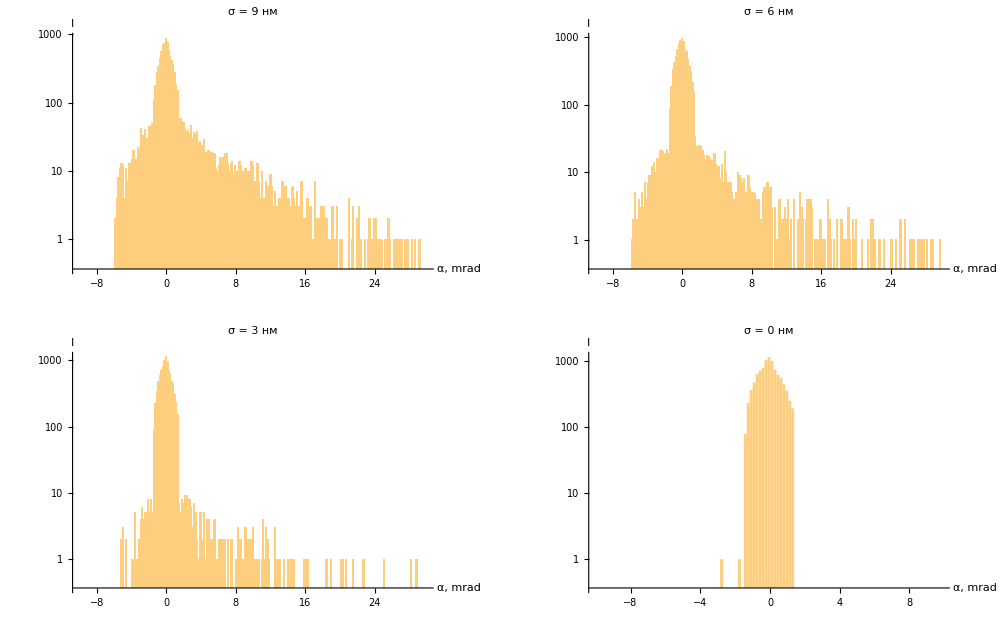

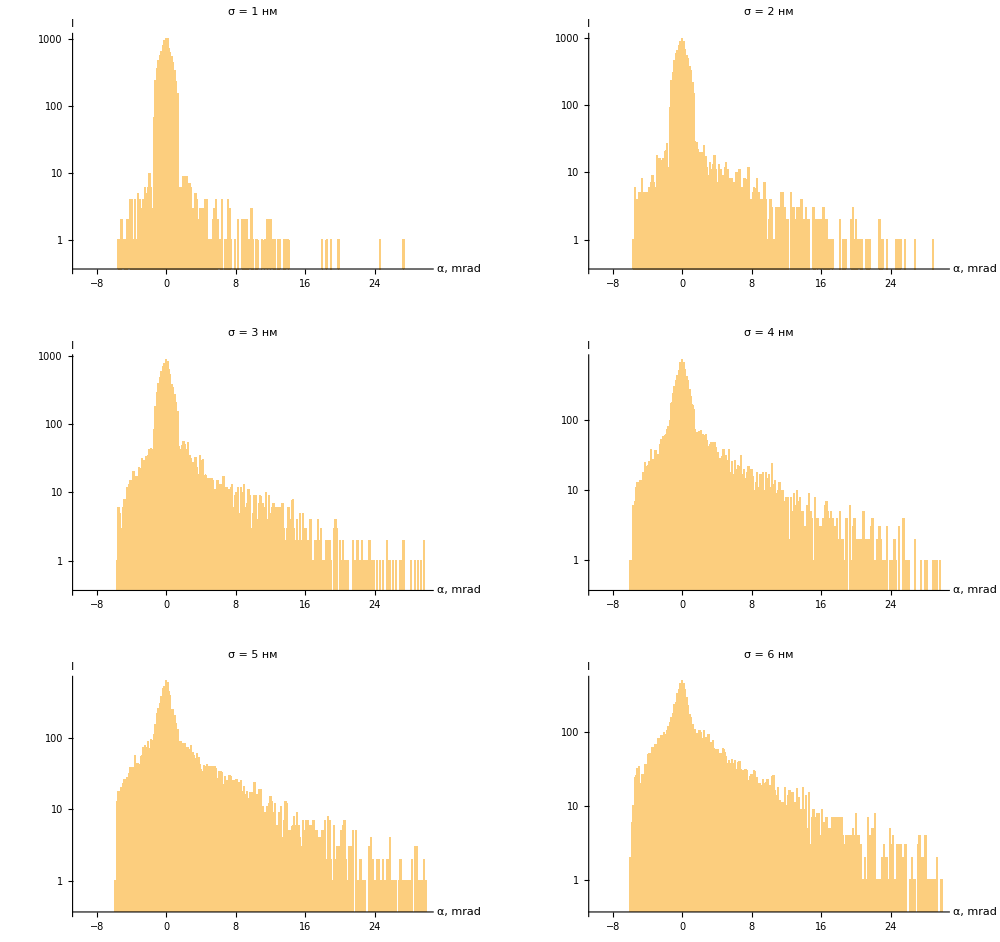

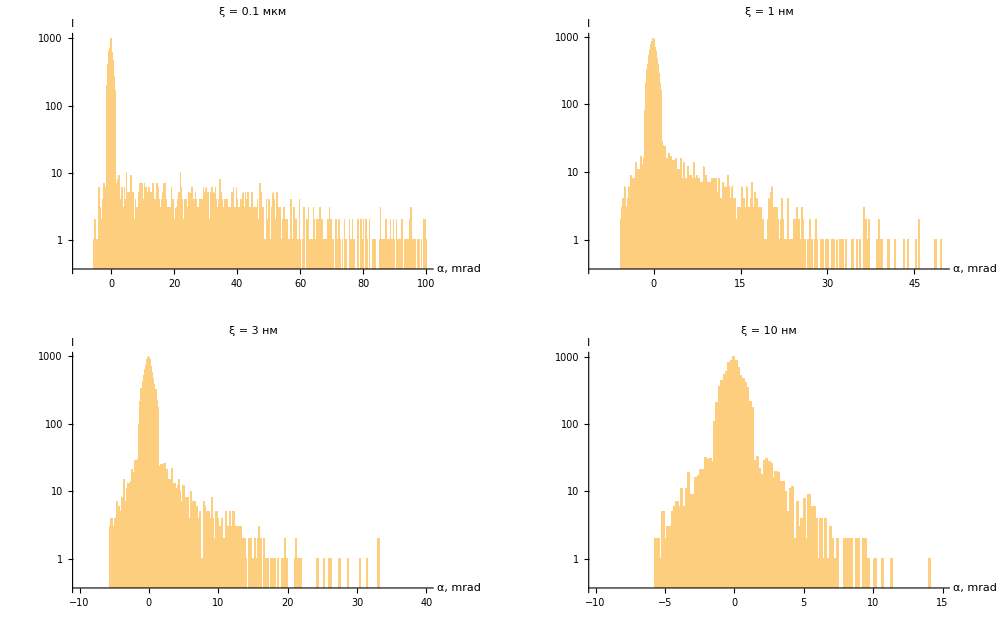

```mathematica
GraphicsGrid[{{Histogram[(results1[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 9 нм",15,Bold,Darker[Red]],AxesStyle->15],Histogram[(results2[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 6 нм",15,Bold,Darker[Red]],AxesStyle->15]},{Histogram[(results3[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 3 нм",15,Bold,Darker[Red]],AxesStyle->15],
Histogram[(results4[[All,3]]-ψ/2)1000,{-10,10,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 0 нм",15,Bold,Darker[Red]],AxesStyle->15]}},ImageSize->1000]
GraphicsGrid[{{Histogram[(results5[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 1 нм",15,Bold,Darker[Red]],AxesStyle->15],Histogram[(results6[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 2 нм",15,Bold,Darker[Red]],AxesStyle->15]},{Histogram[(results7[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 3 нм",15,Bold,Darker[Red]],AxesStyle->15],
Histogram[(results8[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 4 нм",15,Bold,Darker[Red]],AxesStyle->15]},{Histogram[(results9[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 5 нм",15,Bold,Darker[Red]],AxesStyle->15],
Histogram[(results10[[All,3]]-ψ/2)1000,{-10,30,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["σ = 6 нм",15,Bold,Darker[Red]],AxesStyle->15]}},ImageSize->1000]
GraphicsGrid[{{Histogram[(results11[[All,3]]-ψ/2)1000,{-10,100,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["ξ = 0.1 мкм",15,Bold,Darker[Red]],AxesStyle->15],Histogram[(results12[[All,3]]-ψ/2)1000,{-10,50,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["ξ = 1 нм",15,Bold,Darker[Red]],AxesStyle->15]},{Histogram[(results13[[All,3]]-ψ/2)1000,{-10,40,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["ξ = 3 нм",15,Bold,Darker[Red]],AxesStyle->15]
,Histogram[(results15[[All,3]]-ψ/2)1000,{-10,15,0.17},ScalingFunctions->"Log",AxesLabel->{Style["α, mrad",15,Bold],Style["I",15,Bold]},PlotLabel->Style["ξ = 10 нм",15,Bold,Darker[Red]],AxesStyle->15]}},ImageSize->1000]
```

```mathematica
Results Processing
```

```mathematica
dα=1000. √(2dmax/ρ);
resultsξtable={results11,results16,results17,results12,results18,results13,results19,results14,results15};
resultsσtable={results5,results6,results7,results8,results9,results10};
ξtable={0.1,0.3,0.7,1,2,3,4.5,6,10};
dαξtable=2 √(2Log[2])Δ/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,150,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
dαerror=10 √(2Log[2])NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,150,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["ParameterErrors"][[2]]&/@resultsξtable;
dαξlefttable=2 √(2Log[2])Abs[Δ]/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
hξtable=c/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
dασtable=2 √(2Log[2])Δ/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsσtable;
hσtable=c/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsσtable;
herror=4NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["ParameterErrors"][[1]]&/@resultsσtable;
Reffξtable=(Length/@resultsξtable)/10000.;
Reffσtable=(Length/@resultsσtable)/10000.;
```

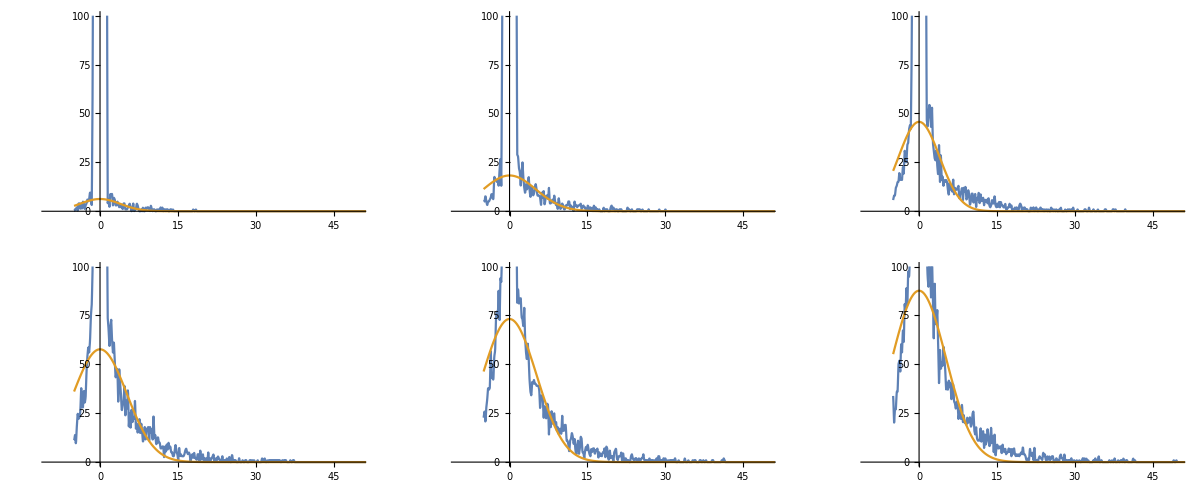

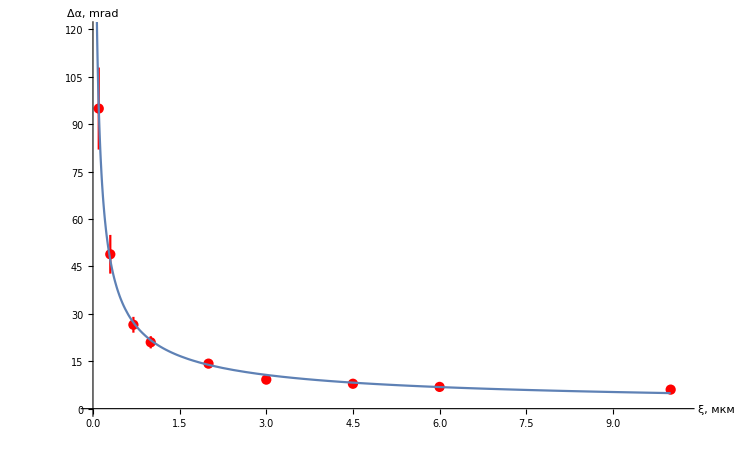

| Estimate | Standard Error | t-Statistic | P-Value
c | 21.6629 | 0.468369 | 46.2519 | 5.77368×10^-10
m | 0.643884 | 0.0107753 | 59.7554 | 9.6491×10^-11

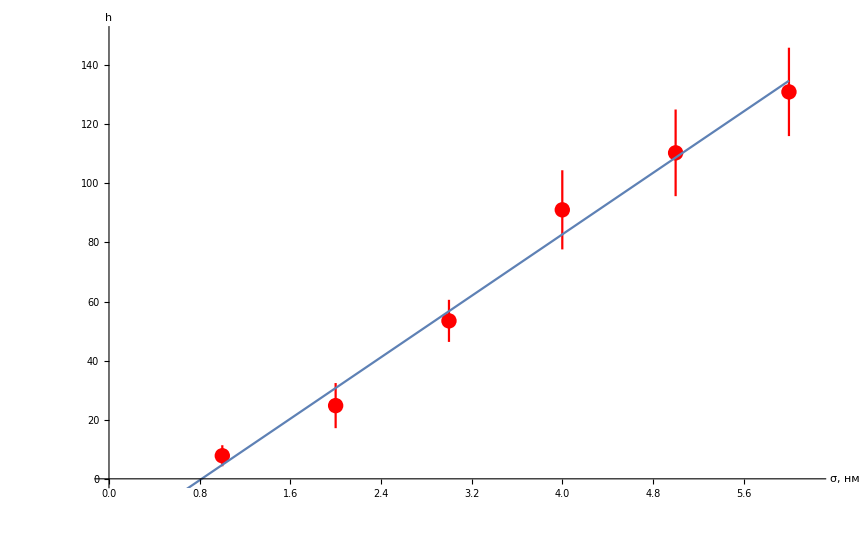

| Estimate | Standard Error | t-Statistic | P-Value
c | 25.9912 | 1.42134 | 18.2864 | 0.0000526055
a | -21.2559 | 5.53533 | -3.84004 | 0.0184589

```mathematica
Needs["ErrorBarPlots`"]
Interpolation[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(results6[[All,3]]-ψ/2)1000],InterpolationOrder->1];
NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(results6[[All,3]]-ψ/2)1000],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x];
GraphicsGrid[Partition[Plot[{Interpolation[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],InterpolationOrder->1][y],NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x][y]}//Evaluate,{y,-5,150},PlotRange->{{-10,50},{0,100}}]&/@resultsσtable,3],ImageSize->Full]
Show[ErrorListPlot[Table[{{ξtable[[i]],dαξtable[[i]]},ErrorBar[dαerror[[i]]]},{i,1,Length[ξtable]}],PlotStyle->{Red,PointSize[0.01]}],Plot[NonlinearModelFit[{ξtable,dαξtable}//Transpose,c/x^m,{c,m},x][y],{y,0,10},PlotRange->All],ImageSize->Medium,AxesStyle->15,AxesLabel->{Style["ξ, мкм",15,Gray],Style["Δα, mrad",15,Gray]},PlotRange->{{0,10.2},{0,120}} ]
NonlinearModelFit[{ξtable,dαξtable}//Transpose,c/x^m,{c,m},x]["ParameterTable"]
Show[ErrorListPlot[{hσtable,herror}//Transpose,ImageSize->Medium,PlotStyle->Red],Plot[NonlinearModelFit[{Range[6],hσtable}//Transpose,c x+a,{c,a},x][y],{y,0,6}],AxesStyle->15,AxesLabel->{Style["σ, нм",15,Gray],Style["h",15,Gray]},PlotRange->{{0,6.2},{0,150}}]
NonlinearModelFit[{Range[6],hσtable}//Transpose,c x+a,{c,a},x]["ParameterTable"]
```

## 3 - Dimensional Case

```mathematica
2-Dimensional PSD-function
```

```mathematica
PSD2D=Mean[Mean[(80/512)^2 Abs[Fourier/@Partition[SurfaceVal 10^-3,{16,16}]//Drop[#,None,None,-Dimensions[#][[3]]/2,-Dimensions[#][[4]]/2]&]^2]];
PSD2Dfunc=GeneralizedLinearModelFit[Table[{Range[0,511/80,511/(80(Dimensions[PSD2D][[1]]-1))][[i]],Range[0,511/80,511/(80(Dimensions[PSD2D][[2]]-1))][[j]],PSD2D[[i,j]]},{i,1,Dimensions[PSD2D][[1]]},{j,1,Dimensions[PSD2D][[2]]}]//Flatten[#,1]&,{x,y,x^2,y^2,x^3,y^3,x^4,y^4,x^5,y^5,x y,x y^2,y x^2,x^2 y^2,x^3 y,x y^3,x^4 y,x^2 y^3,x^3 y^2,x y^4},{x,y},ExponentialFamily->"Binomial"];
PSD2Dmodel:=(10^-6 σ^2 ξ^2 α)/(π(1+(#1^2+#2^2)ξ^2)^(1+α))&
```

```mathematica
ListPlot3D[Log[PSD2D],PlotRange->All]
Plot3D[Log[PSD2Dfunc[x,y]],{x,0,511/80},{y,0,511/80},PlotRange->All]
Plot3D[Log[PSD2Dmodel[x,y]],{x,0,511/80},{y,0,511/80},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
2-Dimensional Scattering Indicatrix
```

```mathematica
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0](*√(Cos[θ0]Cos[θ])*))10^12 PSD2Dmodel[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ]]
AΦ[θinc_,λ_]:=AΦ[θinc,λ]=NIntegrate[Φ[θsc,φsc,θinc,λ]Cos[θsc],{θsc,0,θ0,θinc,π/2},{φsc,-π,π}]
F[θ_,φ_,θ0_,λ_]:=Φ[θ,φ,θ0,λ]/AΦ[θ0,λ]
```

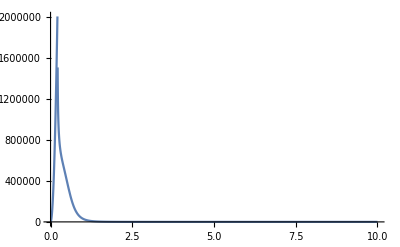

-Graphics3D-

```mathematica
Plot[F[θ °,0,θ0,λ0],{θ,0,10},PlotRange->All]
Plot3D[Log[F[θ °,φ °,50° ,λ0]],{θ,0,90},{φ,-180,180},PlotRange->All]
```

```mathematica
Random Number Generator
```

```mathematica
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<89°,Assumptions->0<θsc<89°,Method->"Normalize"]
distRNG1[y_,len_,prec_:MachinePrecision]:=Module[{x1,x2},
x1=RandomVariate[mydistm[y],len,WorkingPrecision->prec];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->prec]&/@x1;
Transpose[{x1,x2}]
]
```

```mathematica
distRNG1[θ0,10^3]>>sample;
```

```mathematica
sample=<<sample;
Show[Histogram3D[sample,{0.005°},"PDF",PlotRange->All,ChartElementFunction->"GradientScaleCube",ChartStyle->Opacity[0.5]],Plot3D[F[x,y,θ0,λ0],{x,0,1°},{y,-1°,1°},PlotStyle->None,MeshStyle->Thick,PlotRange->All,MaxRecursion->5],PlotRange->{{0,0.5°},{-0.1°,0.1°},{0,2 10^6}}]
```

-Graphics3D-

```mathematica
The Experiment Geometry
```

```mathematica
φmin[y0_]:=ArcTan[-y0/L]-ArcSin[(d/2)/(√(L^2+y0^2))]
φmax[y0_]:=ArcTan[-y0/L]+ArcSin[(d/2)/(√(L^2+y0^2))]
pts1:=Quiet[NSolve[{y==line[x,#],x==d/2Cos[θ],y==d/2Sin[θ]},{x,y,θ}]]&
θmax[y0_,pts1_]:=ArcTan[(Tan[ψ/2](L-d/2))/(√((L+x)^2+(y0-y)^2))/.pts1[[1]]]
θmin[y0_,pts1_]:=ArcTan[(Tan[ψ/2](L-d/2))/(√((L+x)^2+(y0-y)^2))/.pts1[[2]]]
y0=RandomReal[{-100,100}];(* Точка источника луча *)
φinc=RandomReal[{φmin[y0],φmax[y0]}];(* азимутальный угол падения *)
parinc={-L,y0,φinc};
θinc=RandomReal[{-θmax[y0,pts1[parinc]],-θmin[y0,pts1[parinc]]}];(* скользящий угол падения *)
```

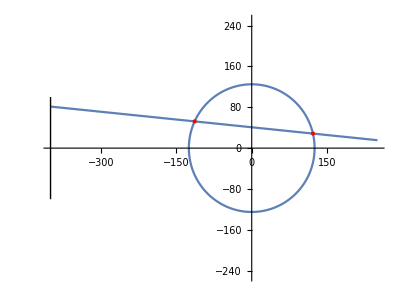

-Graphics3D-

```mathematica
Show[Plot[line[x,parinc],{x,-L,d},PlotRange->All],ParametricPlot[{d/2Cos[θ],d/2Sin[θ]},{θ,0,2π},PlotRange->All],Graphics[{Red,PointSize[Medium],Point[{x,y}/.#]}]&/@pts1[parinc],Graphics[{Black,Line[{{-L,-100},{-L,100}}]}],PlotRange->{{-L,d},{-d,d}},AspectRatio->2d/(L+d),AxesOrigin->{0,0}]
Show[ParametricPlot3D[{ρ Sin[θ]Cos[φ],ρ Sin[θ]Sin[φ],ρ(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π},PlotRange->All],ParametricPlot3D[{-L+Cos[θinc]Cos[φinc]t,y0+Cos[θinc]Sin[φinc]t,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+Sin[θinc]t},{t,0,500},PlotRange->All],ParametricPlot3D[{-L,t,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)},{t,-100,100},PlotRange->All,PlotStyle->Black],BoxRatios->{1,1,1/4},ImageSize->Large]
```

```mathematica
Ray Tracing
```

```mathematica
pts2=Select[NSolve[{x==-L+Cos[θinc]Cos[φinc]s,y==y0+Cos[θinc]Sin[φinc]s,z==ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+Sin[θinc]s,x==ρ Sin[θsph]Cos[φsph],y==ρ Sin[θsph]Sin[φsph],z==ρ(1+Cos[θsph])},{x,y,z,θsph,φsph,s}]//Quiet,π-ψ/2≤(θsph/.#)≤π&][[1]]
α=π/2-VectorAngle[{Cos[θinc]Cos[φinc],Cos[θinc]Sin[φinc],Sin[θinc]},{Sin[θsph]Cos[φsph],Sin[θsph]Sin[φsph],Cos[θsph]}]/.pts2
{θsc,φsc}=distRNG1[π/2-VectorAngle[{Cos[θinc]Cos[φinc],Cos[θinc]Sin[φinc],Sin[θinc]},{Sin[θsph]Cos[φsph],Sin[θsph]Sin[φsph],Cos[θsph]}]/.pts2,1][[1]]
Show[ParametricPlot3D[{ρ Sin[θ]Cos[φ],ρ Sin[θ]Sin[φ],ρ(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π},PlotRange->All],ParametricPlot3D[{-L+Cos[θinc]Cos[φinc]t,y0+Cos[θinc]Sin[φinc]t,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)+Sin[θinc]t},{t,0,550},PlotRange->All],ParametricPlot3D[{-L,t,ρ-Cot[ψ/2]d/2+Tan[ψ/2](L-d/2)},{t,-100,100},PlotRange->All,PlotStyle->Black],Graphics3D[{Green,PointSize[Large],Point[{x,y,z}/.pts2]}],ParametricPlot3D[{x+Cos[θinc+α]Cos[φinc]t,y+Cos[θinc+α]Sin[φinc]t,z+Sin[θinc+α]
t}/.pts2,{t,-100,100},PlotStyle->Orange],ParametricPlot3D[{x+Cos[θinc+α+θsc]Cos[φinc+φsc]t,y+Cos[θinc+α+θsc]Sin[φinc+φsc]t,z+Sin[θinc+α+θsc]
t}/.pts2,{t,0,200},PlotStyle->Green],BoxRatios->{1,1,1/4},ImageSize->Large]
```

{z→0.336443,y→-39.7433,x→108.987,s→508.99,θsph→3.13579,φsph→-2.79192,Sin[θsph]→-0.00580035,Cos[θsph]→-0.999983,Sin[φsph]→0.342594,Cos[φsph]→-0.939484}

0.00893397

{0.00437161,0.0000327957}

-Graphics3D-

```mathematica
initline3D=Module[{y0,φ},
y0=RandomReal[{-100,100}];
φ=RandomReal[{ArcTan[-y0/L]-ArcSin[(d/2)/(√(L^2+y0^2))],ArcTan[-y0/L]+ArcSin[(d/2)/(√(L^2+y0^2))]}];
]
```